# Testing the EP.

L. Amendola and Z. Zheng 2024

This notebook forecasts the relative errors  on several parameters, including the EP-violation parameter Ep, with relativistic corrections. It reads the external file CAMB0.dat (also in this repository) produced with the CAMB code. 
The entire evaluation takes around 20 minutes on a laptop. All the results are stored in the folder outputdir. The final marginalized errors are in “errors”<>labelc<>”.dat” where labelc depends on some choices.

```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
```

## Building the Fisher matrix

```mathematica
(* general choices *)

ClearAll["Global`*"];
Off[Simplify::time];
outputdir="results/";
method="3x2g";
case="DESI";
case="SKA2";
```

```mathematica
expand[x_]:=Simplify[x,TimeConstraint->1];
alpha[hdpar_,dpar_]=1/dpar*Sqrt[mu^2*(hdpar^2-1)+1];
muap=Simplify[mu*hdpar/dpar/alpha[hdpar,dpar]];
kap=alpha[hdpar,dpar]*k;

(* L=F; M=B*)
facgl=1+betal*muap^2;
facgm=1+betam*muap^2;
lambda=Simplify[eps*hfid*hdpar/dpar/kap/(1+z)];

(* wide angle correction *)
 (* nps[k] is P(k) local slope *)
 pwas=1; (* put 0 if you don't want  WA correction  *)
pwa=pwas*(-2/5*I*lambda*(betam-betal)*(1/(edref*hdpar))*(5*muap^3-5/2*muap*(muap^2-1)*nps[k]));

(* diag spectra *)
(* here gamma = alpha - Ep *)
gammam=alpham-ep;
gammal=alphal-ep;

(* lambda^0 *)
pdeldelstar=dd^2*(facgl^2)*betam/betal;

(* lambda^0 *)
pdemdemstar=dd^2*(facgm^2)*betal/betam;

(* cross spectra lambda^1 *)
pdeldemstar=dd^2*((facgl-I*muap*betal*lambda*gammal)*(facgm+I*muap*betam*lambda*gammam)+I*muap*betal*lambda*gammal*I*muap*betam*lambda*gammam)-dd^2*pwa;
pdemdelstar=dd^2*((facgl+I*muap*betal*lambda*gammal)*(facgm-I*muap*betam*lambda*gammam)+I*muap*betal*lambda*gammal*I*muap*betam*lambda*gammam)+dd^2*pwa;



(* shot noise terms; for nn->0 no noise *)
ngl=nn/ndensl/bigb/p[hdpar,dpar];
ngm=nn/ndensm/bigb/p[hdpar,dpar];


(* 3x2g covariance matrix *)

c=expand[p[hdpar,dpar]*bigb*{{pdeldelstar+ngl,pdeldemstar},{pdemdelstar,pdemdemstar+ngm}}];zpar={hdpar,dpar};
zpar={betal,betam,hdpar,dpar,ep,bigb,sigg};  
kzpar={p[hdpar,dpar]};
fixpar={};


(* parameters; we actually use the log of these in the matrix !*)
ppar=Join[kzpar,zpar,fixpar];
pparlog=ppar;

pparnames=Map[ToString,ppar];
Print[pparnames];



npar=Length[ppar];
(* number of params that depend also on k ,  those that deend only on z, and those independent *)
nk=Length[kzpar];
nz=Length[zpar];
n0=Length[fixpar];
n=Length[c];

(* new deriv wrt hd and d *)
rep={p[hdpar,dpar]->p,Derivative[1,0][p][hdpar,dpar]->k mu^2 pder,Derivative[0,1][p][hdpar,dpar]->-k pder}; 
fid1={hdpar->1,dpar->1};


label="-"<>method<>"-np"<>ToString[npar];
labelc=case<>label;
Print[label]

(* useful functions *)
priorblock[parn_,prior_]:=DiagonalMatrix[Table[If[Position[pparnames,parn]!={} && i==Position[pparnames,parn][[1,1]],1/prior^2,0],{i,npar}]];
(* dropping rows and columns *)
drop[m_,parts__List]/;Length@{parts}<=ArrayDepth[m]:=m[[##]]&@@MapThread[Complement,{Range@Dimensions[m,Length@{parts}],{parts}}];
choplevel=10^-8; (* threshold of the relative amplitude of the imaginary part below which it is neglected *)
chopim[x_,r_]:=If[Abs[Im[x]]<r*Abs[Re[x]],Re[x],x];
```

{p[hdpar, dpar],betal,betam,hdpar,dpar,ep,bigb,sigg}

-3x2g-np8

```mathematica
invc=expand[Inverse[c]];
(* smoothing factors *)
dv=Exp[-(1/4)*(k*mu*sigv)^2]; 
dd=Exp[-(1/4)*(k*mu*sigg)^2];

invc>>outputdir<>"invcorr"<>label<>".txt";
c>>outputdir<>"corr"<>label<>".txt";


Monitor[dcp=Table[expand[D[c[[i,j]],ppar[[a]]]/.rep/.fid1],{i,n},{j,n},{a,npar}],a];

(* this cell might take a few minutes *)
invcs=invc/.rep/.fid1;

gammafm=ParallelTable[Quiet[expand[(invcs[[j,m]]*invcs[[l,i]])]],{j,n},{m,n},{l,n},{i,n}];

fmu1=Table[0,{a,npar},{b,npar}];
SetSharedVariable[fmu1];
ParallelDo[{If[a==b,Print[a,", ",b]],fmu1[[a,b]]=Quiet[1/2*expand[Sum[pparlog[[a]]*pparlog[[b]]*dcp[[i,j,a]]*dcp[[m,l,b]]*gammafm[[j,m,l,i]]/.rep/.fid1,{i,n},{j,n},{l,n},{m,n}]]]},{a,npar},{b,a,npar}];
fmu[p_,betal_,betam_,k_,z_,sv2_,sigg_,sigv_,pder_,mu_]=Table[If[b>=a,fmu1[[a,b]],fmu1[[b,a]]],{a,npar},{b,npar}];
fmu1>>outputdir<>"fmu1"<>label<>".txt";
```

1, 1

2, 2

5, 5

6, 6

7, 7

8, 8

3, 3

4, 4

```mathematica
(* if you only need to read the previous correlation and FM elements, execute this cell instead of the previous one
(* ******read already evaluated matrices***** *)

invc=Get["results/invcorr"<>label<>".txt"];
c=Get["results/corr"<>label<>".txt"];
dv=Exp[-(1/4)*(k*mu*sigv)^2]; 
dd=Exp[-(1/4)*(k*mu*sigg)^2];

fmu1=Get["results/fmu1"<>label<>".txt"];
fmu[p_,betal_,betam_,k_,z_,sv2_,sigg_,sigv_,pder_,mu_]=Table[If[b>=a,fmu1[[a,b]],fmu1[[b,a]]],{a,npar},{b,npar}];

*)
```

```mathematica
(* FM summed over mu *)
dmu=0.1;fisheraux[p_,betal_,betam_,k_,z_,sv2_,sigg_,sigv_,pder_]:=dmu*
Table[If[b>a,fmu[p,betal,betam,k,z,sv2,sigg,sigv,pder,0][[a,b]]+2*Sum[fmu[p,betal,betam,k,z,sv2,sigg,sigv,pder,mu][[a,b]],{mu,dmu,1,dmu}],0],{a,1,npar},{b,1,npar}];
(* exploit the symmetry *)
fisher[p_,betal_,betam_,k_,z_,sv2_,sigg_,sigv_,pder_]:=Module[{},mat=fisheraux[p,betal,betam,k,z,sv2,sigg,sigv,pder];mat0=fmu[p,betal,betam,k,z,sv2,sigg,sigv,pder,0];matsum=Sum[fmu[p,betal,betam,k,z,sv2,sigg,sigv,pder,mu],{mu,dmu,1,dmu}];
diag=Table[mat0[[a,a]]+2*matsum[[a,a]],{a,1,npar}];
fm=mat+Transpose[mat]+dmu*DiagonalMatrix[diag];fm];
```

## Fiducials and survey specifics

```mathematica
(* Read power spectrum from CAMB *)
```

```mathematica
PSzero=Import["CAMB0.dat","Table"]; (* norm s8=0.83 *)

PSfunc=Interpolation[PSzero];

ListLogLogPlot[PSfunc,Joined-> True,PlotRange->{{0.001,0.5},{700,30000}},Frame->True];




(* fiducial cosmology and survey specifics *)

Clear[om];
omegam=0.311;
grgam=0.545; (* LCDM growth index *)
(* Hubble function fiducial *)
eh2[z_]=omegam*(1+z)^3+1-omegam;
(* Omega_matter *)
om[z_]=omegam*(1+z)^3/eh2[z];
(* growth rate *)
fgrow[z_,grgam_]=om[z]^grgam;
(* growth factor *)
gr=Interpolation[Table[{z,Exp[-NIntegrate[fgrow[zx,grgam]/(1+zx),{zx,0,z},WorkingPrecision->10,MaxRecursion->12]]},{z,0,2,0.01}]];


(* fiducial luminosity distance and derivative *)
rint=Interpolation[Table[{z,NIntegrate[1/Sqrt[eh2[zint]],{zint,0,z}]},{z,0,2,0.01}]];
dang[z_]:=rint[z]/(1+z);
dlum[z_]:=(1+z)*rint[z];
dlump[z_]:=(1+z)/Sqrt[eh2[z]]+rint[z];

hubble=2997;volume[z1_,z2_]=4*Pi/3*((rint[z2]*hubble)^3-(rint[z1]*hubble)^3);
skygrad=4.*Pi/(Pi/180)^2;

hfidx[z_]=Sqrt[eh2[z]]/2997.;  (* fiducial H_r *)
hph[z_]=-Simplify[(1+z)*D[hfidx[z]/(1+z),z]/(hfidx[z]/(1+z))]; (* fiducial hconf'/hconf *)
edfid[z_]=Sqrt[eh2[z]]*dang[z]; (* E*D *)
hconf[z_]=Sqrt[eh2[z]]/(1+z); (* conf h *)


pskz[k_]:=PSfunc[k];
pskzder[k_]:=D[PSfunc[kx],kx]/.kx->k;



(* galaxy survey data *)


If[case=="DESI",{
(* DESI-Euclid *)
bg={1.38,1.45,1.53,1.61,1.7};
bgf=bg-0.5;
bgb=bg+0.5;
zbins={0.05,0.15,0.25,0.35,0.45};
ndensgvec={40.8,18.7,4.61,0.99,0.11}*10^(-3);
ndensvec={0.096,0.096,0.114,0.1310,0.131}*10^(-3); 

vol={0.04,0.23,0.58,1.04,1.55}*10^9;
slopeb={0.239,0.479,0.820,1.34,2.13};
slopef={-0.071,-0.132,-.174,-.205,-.227};
(* gamma=alpha=1-5s+(5s-2)/Hr-H'/H);*);
alphamv=Table[1-5*slopeb[[i]]+(5*slopeb[[i]]-2)/hconf[zbins[[i]]]/rint[zbins[[i]]],{i,Length[zbins]}]-hph[zbins];
alphalv=Table[1-5*slopef[[i]]+(5*slopef[[i]]-2)/hconf[zbins[[i]]]/rint[zbins[[i]]],{i,Length[zbins]}]-hph[zbins]; 
}]



If[case=="SKA2",{
 zbins={0.25,0.35,0.45,0.55,0.65,0.75};
dz=0.1;fsky=30000/skygrad;
(* LSST 2111.05185*)
ndensvec={0.105,0.114,0.122,0.131,0.139,0.148}*10^(-3); 
(* SKA 1509.07562 table 3; using h=0.67 *)
littleh=0.67;
ndensgvec={3.63,2.16,1.31,0.807,0.511,0.327}*10^(-2)/littleh^3; 
vol=fsky*Table[volume[zbins[[i]]-dz/2,zbins[[i]]+dz/2],{i,Length[zbins]}]; 
bg={0.674,0.730,0.790,0.854,0.922,0.996};
(* l=F, m=B *)
bgf=bg-0.5;
bgb=bg+0.5;
alphamv=1+{-2.84,-1.68,-.99,-.62,-.47,-.42}-hph[zbins];
alphalv=1+{-12.62,-8.84,-6.94,-5.71,-4.82,-4.15}-hph[zbins];
slopeb={0.371,0.442,0.525,0.607,0.682,0.755};
slopef=-{0.162,0.132,0.126,0.125,0.121,0.118};}]




gammafidxb=Interpolation[Table[{zbins[[i]],alphamv[[i]]},{i,Length[zbins]}],InterpolationOrder->1]; (* this is actually alpha *)
gammafidxf=Interpolation[Table[{zbins[[i]],alphalv[[i]]},{i,Length[zbins]}],InterpolationOrder->1];  (* this is actually alpha *)
slopefidxb=Interpolation[Table[{zbins[[i]],slopeb[[i]]},{i,Length[zbins]}],InterpolationOrder->1];
slopefidxf=Interpolation[Table[{zbins[[i]],slopef[[i]]},{i,Length[zbins]}],InterpolationOrder->1];



(* fiducial bias=1  *)
biasg=Interpolation[Table[{zbins[[i]],bg[[i]]},{i,Length[zbins]}],InterpolationOrder->1]; (* galaxy bias *)
biasgf=Interpolation[Table[{zbins[[i]],bgf[[i]]},{i,Length[zbins]}],InterpolationOrder->1]; (* galaxy bias *)
biasgb=Interpolation[Table[{zbins[[i]],bgb[[i]]},{i,Length[zbins]}],InterpolationOrder->1]; (* galaxy bias *)

bigbfid[z_]=biasgf[z]*biasgb[z]*gr[z]^2/(biasgf[zbins[[1]]]*biasgb[zbins[[1]]]*gr[zbins[[1]]]^2);


(* fiducial galaxy beta=f/bias_g *)
betagfidf[z_]=fgrow[z,grgam]/biasgf[z];  
betagfidb[z_]=fgrow[z,grgam]/biasgb[z];  

(* fiducial smoothing velocity in Mpc; values from Howlett 2017 *)
siggfid=4.24; 


(* L=F; M=B*)

mugfid=1;etafid=1;

alpha1l[z_]=(5*slopefidxf[z]-2)/hconf[z]/rint[z];
alpha1m[z_]=(5*slopefidxb[z]-2)/hconf[z]/rint[z];

Print[case]
Print[labelc]

(* spectrum slope *)
nps[k_]=pskzder[k]*k/pskz[k];
```

{Null}

SKA2

SKA2-3x2g-np8

```mathematica
(* Table of fiducials  *)
Print[method];Print[case];
surtab=Table[{zbins[[i]],NumberForm[vol[[i]]*10^-9,3],
NumberForm[ndensgvec[[i]]*10^3,3],NumberForm[biasg[zbins[[i]]],3],NumberForm[slopeb[[i]],3],NumberForm[slopef[[i]],3],NumberForm[betagfidb[zbins[[i]]],3],NumberForm[betagfidf[zbins[[i]]],3],NumberForm[gammafidxb[zbins[[i]]],3],NumberForm[gammafidxf[zbins[[i]]],3],NumberForm[bigbfid[zbins[[i]]],3]},{i,Length[zbins]}];
Print[" z,      V,      n,    bg,        sb,       sf,       betab,   betaf,   alphab,   alphaf,  B"];
surtab//TableForm
(* surtab//TeXForm *)
```

3x2g

SKA2

z,      V,      n,    bg,        sb,       sf,       betab,   betaf,   alphab,   alphaf,  B

0.25 | 1.2 | 121. | 0.674 | 0.371 | -0.162 | 0.563 | 3.8 | -2.14 | -11.9 | 1.
0.35 | 2.1 | 71.8 | 0.73 | 0.442 | -0.132 | 0.573 | 3.06 | -0.891 | -8.05 | 1.25
0.45 | 3.09 | 43.6 | 0.79 | 0.525 | -0.126 | 0.576 | 2.56 | -0.121 | -6.07 | 1.49
0.55 | 4.11 | 26.8 | 0.854 | 0.607 | -0.125 | 0.573 | 2.19 | 0.32 | -4.77 | 1.72
0.65 | 5.11 | 17. | 0.922 | 0.682 | -0.121 | 0.565 | 1.9 | 0.535 | -3.82 | 1.95
0.75 | 6.06 | 10.9 | 0.996 | 0.755 | -0.118 | 0.554 | 1.67 | 0.641 | -3.09 | 2.19

## Fisher in bins

```mathematica
(* creates matrices for every z *)
```

```mathematica
Print["Case: ",case,"; label: ",labelc,"; method: ",method];Clear[nb];
Print[pparnames];
nbins=Length[zbins];

results={};
priorsigma=10; (* prior on the  sigma's *)
priorhd=1000; (* prior on hd *)
priord=0.03; (* prior on d *)
If[priord!= 0.03,labelc=labelc<>ToString[priord]];
priorpi=1000;
priorgamma=1000; (* prior on Ep *)

fullfm=Table[0,{zshell, nbins}];
fullfmnp=Table[0,{zshell, nbins}];

nbv=fullfm;

nz0=nz+n0;
(* prepare the partial FM for every z *)
(* do over z shells *)
SetSharedVariable[fullfm,fullfmnp,savematknp,badbins,badbins2];
badbins={};badbins2={};
(* set up the k-binning *)
dek=0.01;
kmax1=0.12;
kmin1=0.01; 
kbins=Range[kmin1,kmax1,dek];
nb=Length[kbins]; (* number of k bin in shell zshell *)
kbins

(* k-cell gamma^2 factor *)
gam2[k_,V_]:=8*Pi^2/k^2/V/dek;

hdpos=Position[pparnames,"hdpar"][[1,1]];
dpos=Position[pparnames,"dpar"][[1,1]];
bmpos=Position[pparnames,"betam"][[1,1]];

If[Position[pparnames,"ep"]!={},glpos=Position[pparnames,"ep"][[1,1]]];
If[Position[pparnames,"xil"]!={},xilpos=Position[pparnames,"xil"][[1,1]]];

savematknp=Table[0,{i,nb},{zshell,Length[zbins]}];


ParallelDo[{   (* Do over z-bins *)

i=0;

zval=zbins[[zshell]];
ndensl=ndensgvec[[zshell]]/2; 
ndensm=ndensgvec[[zshell]]/2; 
ndensv=ndensvec[[zshell]]; 
hfid=hfidx[zval];
edref=edfid[zval];
pi=pifid[zval];
(* l=F, m=B *);
alphal=gammafidxf[zval];
alpham=gammafidxb[zval];
xil=xilfid[zval];
xim=ximfid[zval];
bigb=bigbfid[zval];
betam=betagfidb[zval];
betal=betagfidf[zval];
ep=1;

Print["z=",zval,"; ndensl=",ndensl,"; hfid=",hfid,"; alphal=",alphal,"; alpham=,",alpham,"; bigb=",bigb,"; betam=",betam,"; betal=",betal];

nkb=nk*nb;
fullmatk=Table[0,{im,nb*nk+nz0},{jm,nb*nk+nz0}];
fullmatknp=fullmatk;
totk=nb*nbins;
eps=1;nn=1;
Do[   (* Do over k-bins *)

{kval=kbins[[i]];

(* add prior to dpar in the z sector, such that when is summed of the k,z bins one gets 1/priorerr^2 fisher[p_,beta_,k_,z_,sv2_,sigg_,sigv_,pder_]*);

matk0=1/gam2[kval,vol[[zshell]]]*fisher[pskz[kval],betal,betam,kval,zval,svx[zval],siggfid,sigvfid,pskzder[kval]];
matknp=Map[chopim[#1,choplevel]&,matk0,{2}];
iout=0; (* if iout=1 then do some tests *);
If[zshell==1 &&  i==iout,{nmatk0=1/gam2[kval,vol[[zshell]]]*nfisher[pskz[kval],betal,betam,kval,zval,svx[zval],siggfid,sigvfid,pskzder[kval]];
nmatknp=Map[chopim[#1,choplevel]&,nmatk0,{2}];tmatk0=1/gam2[kval,vol[[zshell]]]*tfisher[pskz[kval],betal,betam,kval,zval,svx[zval],siggfid,sigvfid,pskzder[kval]];
tmatknp=Map[chopim[#1,choplevel]&,tmatk0,{2}]
}];
matk=matknp+
priorblock["pi",priorpi*Sqrt[nb]]+priorblock["tau1",priorgamma*Sqrt[nb]]+priorblock["tau2",priorgamma*Sqrt[nb]]+priorblock["dpar",priord*Sqrt[nb]]+priorblock["hdpar",priorhd*Sqrt[nb]]+priorblock["sigg",priorsigma*Sqrt[nb]]+priorblock["sigv",priorsigma*Sqrt[nb]]+If[zshell==1,priorblock["bigb",0.0001*Sqrt[nb]],0];
negflag=1;
pflag=1;
(*  discard bins with negative eigenvalues *);
eigen=Map[chopim[#1,choplevel]&,Eigenvalues[matk],{1}];
Do[If[ negflag==1 && (Re[eigen[[i]]]<-10^(-6) || Im[eigen[[i]]]!=0),{negflag=0,If[pflag==1,{Print[{zval,kval,Min[Re[eigen]]}],AppendTo[badbins2,{zval,kval}],pflag=0}]}],{i,Length[Diagonal[matknp]]}];
matk=negflag*matk;
matknp=negflag*matknp;




fullmatk=fullmatk+Table[If[((im≥nk*(i-1)+1 && im≤nk*(i-1)+nk) &&  (jm≥nk*(i-1)+1 && jm≤nk*(i-1)+nk))  
,matk[[im-nk*(i-1),jm-nk*(i-1)]],0],{im,nb*nk+nz0},{jm,nb*nk+nz0}]+
Table[If[
((im≥nk*(i-1)+1 && im≤nk*(i-1)+nk) &&  (jm≥nk*nb+1 && jm<=nk*nb+nz0 )) 
,matk[[im-nk*(i-1),jm-nk*(nb-1)]],0],{im,nb*nk+nz0},{jm,nb*nk+nz0}]+
Table[If[
((jm≥nk*(i-1)+1 && jm≤nk*(i-1)+nk) &&  (im≥nk*nb+1 && im<=nk*nb+nz0 )) 
,matk[[im-nk*(nb-1),jm-nk*(i-1)]],0],{im,nb*nk+nz0},{jm,nb*nk+nz0}]+
Table[If[
((im≥nk*nb+1 && im<=nk*nb+nz0 ) &&  (jm≥nk*nb+1 && jm<=nk*nb+nz0 )) 
,matk[[im-nk*(nb-1),jm-nk*(nb-1)]],0],{im,nb*nk+nz0},{jm,nb*nk+nz0}];

fullmatknp=fullmatknp+Table[If[((im≥nk*(i-1)+1 && im≤nk*(i-1)+nk) &&  (jm≥nk*(i-1)+1 && jm≤nk*(i-1)+nk))  
,matknp[[im-nk*(i-1),jm-nk*(i-1)]],0],{im,nb*nk+nz0},{jm,nb*nk+nz0}]+
Table[If[
((im≥nk*(i-1)+1 && im≤nk*(i-1)+nk) &&  (jm≥nk*nb+1 && jm<=nk*nb+nz0 )) 
,matknp[[im-nk*(i-1),jm-nk*(nb-1)]],0],{im,nb*nk+nz0},{jm,nb*nk+nz0}]+
Table[If[
((jm≥nk*(i-1)+1 && jm≤nk*(i-1)+nk) &&  (im≥nk*nb+1 && im<=nk*nb+nz0 )) 
,matknp[[im-nk*(nb-1),jm-nk*(i-1)]],0],{im,nb*nk+nz0},{jm,nb*nk+nz0}]+
Table[If[
((im≥nk*nb+1 && im<=nk*nb+nz0 ) &&  (jm≥nk*nb+1 && jm<=nk*nb+nz0 )) 
,matknp[[im-nk*(nb-1),jm-nk*(nb-1)]],0],{im,nb*nk+nz0},{jm,nb*nk+nz0}];

savematknp[[i,zshell]]=matknp;

},{i,nb}];fullfm[[zshell]]=fullmatk;fullfmnp[[zshell]]=fullmatknp;



},{zshell,Length[zbins]}];
savematknp>>outputdir<>"kzfmnp-"<>labelc<>".dat";
```

Case: SKA2; label: SKA2-3x2g-np8; method: 3x2g

{p[hdpar, dpar],betal,betam,hdpar,dpar,ep,bigb,sigg}

{0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12}

z=0.25; ndensl=0.0603465; hfid=0.000379915; pi=pifid[0.25]; alphal=-11.9172; alpham=,-2.13719; bigb=1.; betam=0.563492; betal=3.80195; xil=xilfid[0.25]; xim=ximfid[0.25]

z=0.35; ndensl=0.0359087; hfid=0.000402367; pi=pifid[0.35]; alphal=-8.05071; alpham=,-0.890711; bigb=1.24663; betam=0.572953; betal=3.06405; xil=xilfid[0.35]; xim=ximfid[0.35]

z=0.45; ndensl=0.0217779; hfid=0.000426927; pi=pifid[0.45]; alphal=-6.07129; alpham=,-0.121291; bigb=1.4865; betam=0.575608; betal=2.56047; xil=xilfid[0.45]; xim=ximfid[0.45]

z=0.55; ndensl=0.0134159; hfid=0.000453483; pi=pifid[0.55]; alphal=-4.76952; alpham=,0.320482; bigb=1.72116; betam=0.572648; betal=2.1903; xil=xilfid[0.55]; xim=ximfid[0.55]

z=0.65; ndensl=0.00849506; hfid=0.000481921; pi=pifid[0.65]; alphal=-3.81543; alpham=,0.534566; bigb=1.95221; betam=0.565209; betal=1.90457; xil=xilfid[0.65]; xim=ximfid[0.65]

z=0.75; ndensl=0.00543617; hfid=0.000512129; pi=pifid[0.75]; alphal=-3.08871; alpham=,0.641289; bigb=2.19289; betam=0.553577; betal=1.66966; xil=xilfid[0.75]; xim=ximfid[0.75]

{0.65,0.01,-610.804}

{0.55,0.01,-142472.}

{0.45,0.01,-14648.1}

{0.35,0.01,-88.6741}

{0.25,0.01,-552.588}

{0.55,0.02,-613148.}

{0.45,0.02,-1.17261×10^6}

{0.25,0.02,-23698.8}

{0.35,0.02,-38799.3}

{0.45,0.03,-6.43508×10^6}

{0.25,0.03,-12616.3}

{0.35,0.03,-127174.}

{0.25,0.04,-217365.}

{0.35,0.04,-286396.}

{0.25,0.05,-569417.}

{0.25,0.06,-233570.}

{0.25,0.07,-53449.2}

SKA2

3x2g

SKA2-3x2g-np8

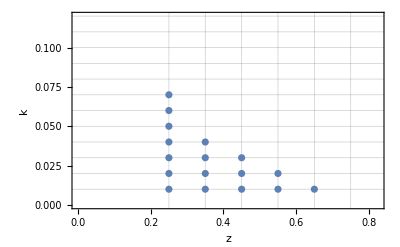

results/badbinsSKA2-3x2g-np8.dat

```mathematica
(* bins that have been discarded *)

Print[case];Print[method];
Print[labelc];ListPlot[badbins2,Frame->True,FrameLabel->{"z","k"},PlotRange->{{0.,1.1*zbins[[-1]]},{0,kmax1}},GridLines->{zbins,kbins}]
Export[outputdir<>"badbins"<>labelc<>".dat",Sort[badbins2],"Table"]
```

## Final Fisher

```mathematica
amat=Table[0,{zshell,Length[zbins]}];bmat=amat;cmat=amat;
Do[{
ffm=fullfm[[zshell]];
dimffm=Length[ffm];
amat[[zshell]]=ffm[[1;;nb,1;;nb]];
bmat[[zshell]]=ffm[[1;;nb,nb+1;;dimffm]];
cmat[[zshell]]=ffm[[nb+1;;dimffm,nb+1;;dimffm]];

},{zshell,Length[zbins]}]
fullbmat={};Do[fullbmat=Join[fullbmat,Transpose[bmat[[i]]]],{i,Length[zbins]}]
totalfm1=ArrayFlatten[{{Total[amat],Transpose[fullbmat]},{fullbmat,BlockDiagonalMatrix[cmat]}}];
totalfm=Map[chopim[#1,choplevel]&,totalfm1,{2}];

Export[outputdir<>"fullfm-"<>labelc<>".dat",totalfm,"Table"];


amat=Table[0,{zshell,Length[zbins]}];bmat=amat;cmat=amat;
Do[{
ffm=fullfmnp[[zshell]];
dimffm=Length[ffm];
amat[[zshell]]=ffm[[1;;nb,1;;nb]];
bmat[[zshell]]=ffm[[1;;nb,nb+1;;dimffm]];
cmat[[zshell]]=ffm[[nb+1;;dimffm,nb+1;;dimffm]];

},{zshell,Length[zbins]}]
fullbmat={};Do[fullbmat=Join[fullbmat,Transpose[bmat[[i]]]],{i,Length[zbins]}]
totalfmnp1=ArrayFlatten[{{Total[amat],Transpose[fullbmat]},{fullbmat,BlockDiagonalMatrix[cmat]}}];
totalfmnp=Map[chopim[#1,choplevel]&,totalfmnp1,{2}];
Export[outputdir<>"fullfmnp-"<>labelc<>".dat",totalfmnp,"Table"];

Map[chopim[#1,choplevel]&,Eigenvalues[totalfm],{1}]
(* MatrixPlot[totalfm]
MatrixPlot[totalfmnp]*)
```

{4.16845×10^7,9.30303×10^6,9.11344×10^6,8.78862×10^6,8.04023×10^6,7.11756×10^6,6.98592×10^6,242185.,227753.,183421.,154125.,146501.,140650.,137455.,126220.,124353.,120169.,100837.,74821.1,72686.3,64825.6,59221.,48788.7,43563.2,39711.9,35714.2,32690.4,26460.2,20694.1,13935.6,10817.4,9208.96,4671.01,3817.19,2823.36,2345.92,1980.01,1612.88,850.287,689.078,384.203,193.621,169.264,140.505,112.387,105.645,87.2393,71.5611,68.1387,59.6771,46.7785,40.4348,33.532,28.2672}

```mathematica
(* finalize results and write output *)
Print[method];
Print[case];
Print[labelc];
dimfm=Length[totalfm];

fullmatz=totalfm;
sumfm1=Inverse[fullmatz];
sumfm=Map[chopim[#1,choplevel]&,sumfm1,{2}];

sumfmi1=PseudoInverse[fullmatz]; (* gives same result as Inverse *);
sumfmi=Map[chopim[#1,choplevel]&,sumfmi1,{2}];

Print["mismatch? =",MinMax[Abs[sumfmi]-Abs[sumfm]]];
param="betal";
If[MemberQ[pparnames,param],{pos=Position[pparnames,param][[1,1]]-1;
errors=Table[Sqrt[sumfm[[  nb+(i-1)*nz+pos,nb+(i-1)*nz+pos ]]],{i,nbins}];
Print[param," ",Table[{zbins[[i]],errors[[i]]},{i,nbins}]//TableForm]}];
param="betam";
If[MemberQ[pparnames,param],{pos=Position[pparnames,param][[1,1]]-1;
errors=Table[Sqrt[sumfm[[  nb+(i-1)*nz+pos,nb+(i-1)*nz+pos ]]],{i,nbins}];
Print[param," ",Table[{zbins[[i]],errors[[i]]},{i,nbins}]//TableForm]}];

param="hdpar";
pos=Position[pparnames,param][[1,1]]-1;
errors=Table[Sqrt[sumfm[[  nb+(i-1)*nz+pos,nb+(i-1)*nz+pos ]]],{i,nbins}];
Print[param," ",Table[{zbins[[i]],errors[[i]]},{i,nbins}]//TableForm];

param="dpar";
pos=Position[pparnames,param][[1,1]]-1;
errors=Table[Sqrt[sumfm[[  nb+(i-1)*nz+pos,nb+(i-1)*nz+pos ]]],{i,nbins}];
Print[param," ",Table[{zbins[[i]],errors[[i]]},{i,nbins}]//TableForm];

param="ep";
pos=Position[pparnames,param][[1,1]]-1;
errors=Table[Sqrt[sumfm[[  nb+(i-1)*nz+pos,nb+(i-1)*nz+pos ]]],{i,nbins}];
Print[param," ",Table[{zbins[[i]],errors[[i]]},{i,nbins}]//TableForm];



finerrors=Sqrt[Diagonal[sumfm]];
finaltable=Join[Table[{"p ",kbins[[i]],NumberForm[finerrors[[i]],4]},{i,nb}],Flatten[Table[{zbins[[j]],pparnames[[i+1]],NumberForm[finerrors[[nb+(j-1)*(npar-1)+i]],4]},{j,Length[zbins]},{i,1,npar-1}],1]];

Export[outputdir<>"errors"<>labelc<>".dat",finaltable,"Table"]
```

3x2g

SKA2

SKA2-3x2g-np8

mismatch? ={-8.37083×10^-15,5.96641×10^-14}

betal 0.25 | 0.00301958
0.35 | 0.00238655
0.45 | 0.00241534
0.55 | 0.00260844
0.65 | 0.00295035
0.75 | 0.00346674

betam 0.25 | 0.00148921
0.35 | 0.00138985
0.45 | 0.00159784
0.55 | 0.00187232
0.65 | 0.00224563
0.75 | 0.00275611

hdpar 0.25 | 0.00203624
0.35 | 0.00199179
0.45 | 0.00230815
0.55 | 0.00270378
0.65 | 0.00323198
0.75 | 0.00393656

dpar 0.25 | 0.0262324
0.35 | 0.021158
0.45 | 0.0196433
0.55 | 0.0185512
0.65 | 0.0177917
0.75 | 0.0173371

ep 0.25 | 0.117297
0.35 | 0.0970539
0.45 | 0.129223
0.55 | 0.146127
0.65 | 0.156974
0.75 | 0.165361

results/errorsSKA2-3x2g-np8.dat